这是原函数

```mathematica
x0=0.;
y0=3.;
fun=1/(N@π)ⅇ^(-Abs[2α-α0]^2);
Qfun[x_,y_]:=Re@fun/.{α->x+ⅈ y,α0->x0+ⅈ y0};
Plot3D[Qfun[x,y],{x,-π,π},{y,0,π},ColorFunction->"TemperatureMap",PlotRange->All,PlotPoints->80,ImageSize->400,
		AxesLabel->{Style["Re[α]",FontFamily->"Times",FontSize->15,FontColor->Black],Style["Im[α]",FontFamily->"Times",FontSize->15,FontColor->Black]}]
```

-Graphics3D-

想把它画在球面上

```mathematica
Q[θ_,ϕ_]:=Qfun[θ,ϕ];
Qmax=NMaximize[Q[x,y],{x,y}][[1]];
Qfunc=ParametricPlot3D[ {Cos[ ϕ] Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]},{ϕ,-π,π}, {θ, 0,π},PlotPoints -> 100,
	                   Mesh->{7,7},MeshStyle->Directive[Thick,Gray],PlotStyle->Opacity[0.95],
	                   ColorFunction->Function[{x,y,z, ϕ, θ},ColorData["DarkRainbow"][Q[θ,ϕ]/Qmax]],
	                   ColorFunctionScaling->False,
	                   Boxed->False,
	                   Axes->False,
	                   ViewPoint->{0,1,1}]
```

-Graphics3D-

画出来应该这个样子才合适

#### 如果不是函数是三维数据点又如何画在球面上呢？

```mathematica
data={{0.,-3.141592653589793,2.0906445767000624*^-12},{0.15,-3.141592653589793,3.7954251667167355*^-10},{0.3,-3.141592653589793,4.690876632843816*^-8},{0.44999999999999996,-3.141592653589793,1.213369994725483*^-6},{0.6,-3.141592653589793,9.281913465739532*^-6},{0.75,-3.141592653589793,0.00002691527437305134},{0.8999999999999999,-3.141592653589793,0.00003396629590477911},{1.05,-3.141592653589793,0.000020067909667639517},{1.2,-3.141592653589793,5.72893675539217*^-6},{1.3499999999999999,-3.141592653589793,7.846884568963238*^-7},{1.5,-3.141592653589793,6.73054897004018*^-8},{1.65,-3.141592653589793,7.50376840861079*^-8},{1.7999999999999998,-3.141592653589793,8.950354614562303*^-7},{1.95,-3.141592653589793,6.2646386433481795*^-6},{2.1,-3.141592653589793,0.00002107315495008653},{2.25,-3.141592653589793,0.000034221964941339956},{2.4,-3.141592653589793,0.00002594454332903708},{2.55,-3.141592653589793,8.51129058334207*^-6},{2.6999999999999997,-3.141592653589793,1.0474080836666134*^-6},{2.85,-3.141592653589793,3.742923324874985*^-8},{3.,-3.141592653589793,2.769249718169507*^-10},{0.,-2.991592653589793,2.0906445767000624*^-12},{0.15,-2.991592653589793,4.535703026396363*^-10},{0.3,-2.991592653589793,4.0742970192663785*^-8},{0.44999999999999996,-2.991592653589793,7.927109688643997*^-7},{0.6,-2.991592653589793,4.795603887961596*^-6},{0.75,-2.991592653589793,0.000011376325030119812},{0.8999999999999999,-2.991592653589793,0.000012011287131564353},{1.05,-2.991592653589793,6.025832883510569*^-6},{1.2,-2.991592653589793,1.4751225347940916*^-6},{1.3499999999999999,-2.991592653589793,1.859513742419904*^-7},{1.5,-2.991592653589793,1.2310926618334902*^-8},{1.65,-2.991592653589793,2.8262163842101697*^-7},{1.7999999999999998,-2.991592653589793,3.7656315679136875*^-6},{1.95,-2.991592653589793,0.000022466727547367026},{2.1,-2.991592653589793,0.00006458194920598543},{2.25,-2.991592653589793,0.00008871151303676994},{2.4,-2.991592653589793,0.000055980159072717525},{2.55,-2.991592653589793,0.00001491806944949069},{2.6999999999999997,-2.991592653589793,1.4367588603188673*^-6},{2.85,-2.991592653589793,3.7991375737588955*^-8},{3.,-2.991592653589793,2.0288776509867435*^-10},{0.,-2.8415926535897933,2.0906445767000624*^-12},{0.15,-2.8415926535897933,4.876354732157595*^-10},{0.3,-2.8415926535897933,3.2048037481094715*^-8},{0.44999999999999996,-2.8415926535897933,4.7376422901569877*^-7},{0.6,-2.8415926535897933,2.281964268754381*^-6},{0.75,-2.8415926535897933,4.449876198899441*^-6},{0.8999999999999999,-2.8415926535897933,3.945079993234656*^-6},{1.05,-2.8415926535897933,1.6858501067617552*^-6},{1.2,-2.8415926535897933,3.554291074661241*^-7},{1.3499999999999999,-2.8415926535897933,2.5637338580832004*^-8},{1.5,-2.8415926535897933,5.8331535146697494*^-8},{1.65,-2.8415926535897933,1.35567939665968*^-6},{1.7999999999999998,-2.8415926535897933,0.00001459963562809341},{1.95,-2.8415926535897933,0.00007479330770802096},{2.1,-2.8415926535897933,0.00018322751834194293},{2.25,-2.8415926535897933,0.0002121477877647128},{2.4,-2.8415926535897933,0.00011093537089523208},{2.55,-2.8415926535897933,0.000023868350801786026},{2.6999999999999997,-2.8415926535897933,1.7824375255616802*^-6},{2.85,-2.8415926535897933,3.4308625629158937*^-8},{3.,-2.8415926535897933,1.2964077775188824*^-10},{0.,-2.691592653589793,2.0906445767000624*^-12},{0.15,-2.691592653589793,4.772505365622485*^-10},{0.3,-2.691592653589793,2.301296116648947*^-8},{0.44999999999999996,-2.691592653589793,2.605042386620568*^-7},{0.6,-2.691592653589793,1.0047113309438267*^-6},{0.75,-2.691592653589793,1.6172401295873101*^-6},{0.8999999999999999,-2.691592653589793,1.207867432266041*^-6},{1.05,-2.691592653589793,4.4043324192827986*^-7},{1.2,-2.691592653589793,7.770057681868676*^-8},{1.3499999999999999,-2.691592653589793,2.3963878171463443*^-8},{1.5,-2.691592653589793,2.77559163547883*^-7},{1.65,-2.691592653589793,5.621681174531341*^-6},{1.7999999999999998,-2.691592653589793,0.000052616322119120486},{1.95,-2.691592653589793,0.00023059160653183085},{2.1,-2.691592653589793,0.0004799569271960173},{2.25,-2.691592653589793,0.00046668954360360354},{2.4,-2.691592653589793,0.000201264596703539},{2.55,-2.691592653589793,0.00003473055207693618},{2.6999999999999997,-2.691592653589793,1.9903149955079594*^-6},{2.85,-2.691592653589793,2.734015768563992*^-8},{3.,-2.691592653589793,7.05624694249656*^-11},{0.,-2.541592653589793,2.0906445767000624*^-12},{0.15,-2.541592653589793,4.295141421409762*^-10},{0.3,-2.541592653589793,1.5201293625863856*^-8},{0.44999999999999996,-2.541592653589793,1.3254690490514168*^-7},{0.6,-2.541592653589793,4.1124974091581593*^-7},{0.75,-2.541592653589793,5.48386371498102*^-7},{0.8999999999999999,-2.541592653589793,3.459820396432456*^-7},{1.05,-2.541592653589793,1.0820699139568037*^-7},{1.2,-2.541592653589793,2.0659285647433575*^-8},{1.3499999999999999,-2.541592653589793,2.1898213069950423*^-8},{1.5,-2.541592653589793,1.2288572364167716*^-6},{1.65,-2.541592653589793,0.000021969814542506675},{1.7999999999999998,-2.541592653589793,0.0001756548853674193},{1.95,-2.541592653589793,0.0006568495468354051},{2.1,-2.541592653589793,0.0011579891645139573},{2.25,-2.541592653589793,0.0009419763549047133},{2.4,-2.541592653589793,0.00033336217826993074},{2.55,-2.541592653589793,0.00004581377680822184},{2.6999999999999997,-2.541592653589793,1.9922544891383158*^-6},{2.85,-2.541592653589793,1.908864439078217*^-8},{3.,-2.541592653589793,3.165429983786493*^-11},{0.,-2.391592653589793,2.0906445767000624*^-12},{0.15,-2.391592653589793,3.586008480229944*^-10},{0.3,-2.391592653589793,9.303938710226587*^-9},{0.44999999999999996,-2.391592653589793,6.276331031882632*^-8},{0.6,-2.391592653589793,1.5725181079036976*^-7},{0.75,-2.391592653589793,1.7423305500317845*^-7},{0.8999999999999999,-2.391592653589793,9.313822648013199*^-8},{1.05,-2.391592653589793,2.4967530178967323*^-8},{1.2,-2.391592653589793,5.178519582382579*^-10},{1.3499999999999999,-2.391592653589793,1.5154929525131726*^-7},{1.5,-2.391592653589793,5.247513842015187*^-6},{1.65,-2.391592653589793,0.00007935825252401394},{1.7999999999999998,-2.391592653589793,0.0005421604268634433},{1.95,-2.391592653589793,0.0017252526911739066},{2.1,-2.391592653589793,0.002567948254275377},{2.25,-2.391592653589793,0.001740697092538549},{2.4,-2.391592653589793,0.0005029267574388491},{2.55,-2.391592653589793,0.00005464589483207693},{2.6999999999999997,-2.391592653589793,1.7821063705874932*^-6},{2.85,-2.391592653589793,1.1616810447465774*^-8},{3.,-2.391592653589793,1.1135372057487403*^-11},{0.,-2.241592653589793,2.0906445767000624*^-12},{0.15,-2.241592653589793,2.79930984817456*^-10},{0.3,-2.241592653589793,5.312533380970361*^-9},{0.44999999999999996,-2.241592653589793,2.7813913716308667*^-8},{0.6,-2.241592653589793,5.644324599268616*^-8},{0.75,-2.241592653589793,5.209520532315073*^-8},{0.8999999999999999,-2.241592653589793,2.358255553889786*^-8},{1.05,-2.241592653589793,5.182439498494195*^-9},{1.2,-2.241592653589793,1.3817012848171339*^-8},{1.3499999999999999,-2.241592653589793,6.733324643028146*^-7},{1.5,-2.241592653589793,0.00002052922126427679},{1.65,-2.241592653589793,0.00026530249783188637},{1.7999999999999998,-2.241592653589793,0.0015444435455917707},{1.95,-2.241592653589793,0.004170961313778627},{2.1,-2.241592653589793,0.005224843523110393},{2.25,-2.241592653589793,0.002939629896685112},{2.4,-2.241592653589793,0.0006898129152758807},{2.55,-2.241592653589793,0.00005882574310937008},{2.6999999999999997,-2.241592653589793,1.421695849864322*^-6},{2.85,-2.241592653589793,6.147895183162502*^-9},{3.,-2.241592653589793,2.8286746630861025*^-12},{0.,-2.0915926535897933,2.0906445767000624*^-12},{0.15,-2.0915926535897933,2.0576762264679283*^-10},{0.3,-2.0915926535897933,2.848368140823567*^-9},{0.44999999999999996,-2.0915926535897933,1.1599078425269152*^-8},{0.6,-2.0915926535897933,1.9109393418098373*^-8},{0.75,-2.0915926535897933,1.471904632196306*^-8},{0.8999999999999999,-2.0915926535897933,5.712057023299017*^-9},{1.05,-2.0915926535897933,1.909618176791924*^-9},{1.2,-2.0915926535897933,3.924541267240575*^-8},{1.3499999999999999,-2.0915926535897933,2.887260915653842*^-6},{1.5,-2.0915926535897933,0.00007456146536356243},{1.65,-2.0915926535897933,0.0008192209642886924},{1.7999999999999998,-2.0915926535897933,0.004054411188363702},{1.95,-2.0915926535897933,0.009267587209570107},{2.1,-2.0915926535897933,0.009739344596878185},{2.25,-2.0915926535897933,0.004530349288897793},{2.4,-2.0915926535897933,0.0008590307766806152},{2.55,-2.0915926535897933,0.00005708097642020065},{2.6999999999999997,-2.0915926535897933,1.0105504548694367*^-6},{2.85,-2.0915926535897933,2.831081281493426*^-9},{3.,-2.0915926535897933,4.5026590604279814*^-13},{0.,-1.9415926535897932,2.0906445767000624*^-12},{0.15,-1.9415926535897932,1.43357110215745*^-10},{0.3,-1.9415926535897932,1.4428395183177997*^-9},{0.44999999999999996,-1.9415926535897932,4.576314492133504*^-9},{0.6,-1.9415926535897932,6.131551507295773*^-9},{0.75,-1.9415926535897932,3.9515504577791806*^-9},{0.8999999999999999,-1.9415926535897932,1.2747295337558373*^-9},{1.05,-1.9415926535897932,6.589034856802625*^-10},{1.2,-1.9415926535897932,2.0786430736449116*^-7},{1.3499999999999999,-1.9415926535897932,0.000011455444990894777},{1.5,-1.9415926535897932,0.000250172115208473},{1.65,-1.9415926535897932,0.0023335259528831846},{1.7999999999999998,-1.9415926535897932,0.009795683728385882},{1.95,-1.9415926535897932,0.01890208017964595},{2.1,-1.9415926535897932,0.016613287042424367},{2.25,-1.9415926535897932,0.006364846144085138},{2.4,-1.9415926535897932,0.0009704131800823907},{2.55,-1.9415926535897932,0.00004989711105633753},{2.6999999999999997,-1.9415926535897932,6.400536545114705*^-7},{2.85,-1.9415926535897932,1.1372227377495209*^-9},{3.,-1.9415926535897932,4.6997657909121735*^-14},{0.,-1.7915926535897932,2.0906445767000624*^-12},{0.15,-1.7915926535897932,9.523802642625834*^-11},{0.3,-1.7915926535897932,6.945593210732437*^-10},{0.44999999999999996,-1.7915926535897932,1.717136770441619*^-9},{0.6,-1.7915926535897932,1.8734555722976726*^-9},{0.75,-1.7915926535897932,1.0065012097557325*^-9},{0.8999999999999999,-1.7915926535897932,2.970040374864434*^-10},{1.05,-1.7915926535897932,7.495177683317619*^-9},{1.2,-1.7915926535897932,8.920451279189574*^-7},{1.3499999999999999,-1.7915926535897932,0.0000419995855480694},{1.5,-1.7915926535897932,0.0007750670471633168},{1.65,-1.7915926535897932,0.006124546333339624},{1.7999999999999998,-1.7915926535897932,0.021758373150837517},{1.95,-1.7915926535897932,0.03535415737592802},{2.1,-1.7915926535897932,0.02591074253753164},{2.25,-1.7915926535897932,0.008146356812408674},{2.4,-1.7915926535897932,0.0009939999368137962},{2.55,-1.7915926535897932,0.0000392931166045698},{2.6999999999999997,-1.7915926535897932,3.6155454837589494*^-7},{2.85,-1.7915926535897932,3.99876841625501*^-10},{3.,-1.7915926535897932,1.9209296450913532*^-14},{0.,-1.6415926535897931,2.0906445767000624*^-12},{0.15,-1.6415926535897931,6.06775697155798*^-11},{0.3,-1.6415926535897931,3.195238688482938*^-10},{0.44999999999999996,-1.6415926535897931,6.158831130615696*^-10},{0.6,-1.6415926535897931,5.475251465787359*^-10},{0.75,-1.6415926535897931,2.5114653251926805*^-10},{0.8999999999999999,-1.6415926535897931,1.6271764430425266*^-10},{1.05,-1.6415926535897931,3.096891741824803*^-8},{1.2,-1.6415926535897931,3.6199899579663362*^-6},{1.3499999999999999,-1.6415926535897931,0.0001423282856554203},{1.5,-1.6415926535897931,0.0022145866621323344},{1.65,-1.6415926535897931,0.014796624125212762},{1.7999999999999998,-1.6415926535897931,0.04439420470789282},{1.95,-1.6415926535897931,0.060595131601417364},{2.1,-1.6415926535897931,0.03692757223489154},{2.25,-1.6415926535897931,0.009495122726537053},{2.4,-1.6415926535897931,0.0009231627183444302},{2.55,-1.6415926535897931,0.000027888424493571778},{2.6999999999999997,-1.6415926535897931,1.824312847793924*^-7},{2.85,-1.6415926535897931,1.2372888455579798*^-10},{3.,-1.6415926535897931,9.778146588455082*^-15},{0.,-1.4915926535897932,2.0906445767000624*^-12},{0.15,-1.4915926535897932,3.7275915713878447*^-11},{0.3,-1.4915926535897932,1.4123450340891119*^-10},{0.44999999999999996,-1.4915926535897932,2.1220205597678605*^-10},{0.6,-1.4915926535897932,1.5391046472547601*^-10},{0.75,-1.4915926535897932,5.448811971837509*^-11},{0.8999999999999999,-1.4915926535897932,4.066577353368215*^-10},{1.05,-1.4915926535897932,1.453717641523121*^-7},{1.2,-1.4915926535897932,0.000013537199056615313},{1.3499999999999999,-1.4915926535897932,0.00044513416143596466},{1.5,-1.4915926535897932,0.005830601776218088},{1.65,-1.4915926535897932,0.03287984910561696},{1.7999999999999998,-1.4915926535897932,0.08314577326909241},{1.95,-1.4915926535897932,0.0951203054072812},{2.1,-1.4915926535897932,0.048075429068509326},{2.25,-1.4915926535897932,0.010077777662326398},{2.4,-1.4915926535897932,0.0007776007870664788},{2.55,-1.4915926535897932,0.00001785571572154849},{2.6999999999999997,-1.4915926535897932,8.238632525836063*^-8},{2.85,-1.4915926535897932,3.385278844511397*^-11},{3.,-1.4915926535897932,3.620764364599087*^-15},{0.,-1.3415926535897933,2.0906445767000624*^-12},{0.15,-1.3415926535897933,2.219583741912067*^-11},{0.3,-1.3415926535897933,6.029560067867603*^-11},{0.44999999999999996,-1.3415926535897933,7.05775153585561*^-11},{0.6,-1.3415926535897933,4.158126016476627*^-11},{0.75,-1.3415926535897933,1.9084771185697645*^-11},{0.8999999999999999,-1.3415926535897933,2.3642590444084716*^-9},{1.05,-1.3415926535897933,6.046259124360069*^-7},{1.2,-1.3415926535897933,0.00004677498454313304},{1.3499999999999999,-1.3415926535897933,0.0012838571584250847},{1.5,-1.3415926535897933,0.014133885683091001},{1.65,-1.3415926535897933,0.06715716266882707},{1.7999999999999998,-1.3415926535897933,0.14287232489947188},{1.95,-1.3415926535897933,0.13671052654665242},{2.1,-1.3415926535897933,0.05716696022479474},{2.25,-1.3415926535897933,0.009741502380063393},{2.4,-1.3415926535897933,0.0005943786543637575},{2.55,-1.3415926535897933,0.00001032486652024137},{2.6999999999999997,-1.3415926535897933,3.33758152550586*^-8},{2.85,-1.3415926535897933,8.192438472354007*^-12},{3.,-1.3415926535897933,3.8369803202068656*^-15},{0.,-1.1915926535897932,2.0906445767000624*^-12},{0.15,-1.1915926535897932,1.2874966237057077*^-11},{0.3,-1.1915926535897932,2.4988402354706*^-11},{0.44999999999999996,-1.1915926535897932,2.2766655129676194*^-11},{0.6,-1.1915926535897932,1.115666065611672*^-11},{0.75,-1.1915926535897932,1.0501174960917311*^-11},{0.8999999999999999,-1.1915926535897932,1.0916683175548251*^-8},{1.05,-1.1915926535897932,2.343759926116134*^-6},{1.2,-1.1915926535897932,0.00014912831343407513},{1.3499999999999999,-1.1915926535897932,0.0034120333923460945},{1.5,-1.1915926535897932,0.03152479066037384},{1.65,-1.1915926535897932,0.12601611507719818},{1.7999999999999998,-1.1915926535897932,0.22516216665560546},{1.95,-1.1915926535897932,0.1798667582808327},{2.1,-1.1915926535897932,0.06209313890545285},{2.25,-1.1915926535897932,0.008579067378665657},{2.4,-1.1915926535897932,0.00041260183768410347},{2.55,-1.1915926535897932,5.3993996533224144*^-6},{2.6999999999999997,-1.1915926535897932,1.2158410713022958*^-8},{2.85,-1.1915926535897932,1.7828820744654712*^-12},{3.,-1.1915926535897932,5.1305318911525524*^-15},{0.,-1.041592653589793,2.0906445767000624*^-12},{0.15,-1.041592653589793,7.311175826043381*^-12},{0.3,-1.041592653589793,1.0102994343408056*^-11},{0.44999999999999996,-1.041592653589793,7.157410515197944*^-12},{0.6,-1.041592653589793,2.561667288364367*^-12},{0.75,-1.041592653589793,6.876663128585272*^-11},{0.8999999999999999,-1.041592653589793,4.87383716016813*^-8},{1.05,-1.041592653589793,8.372672181474732*^-6},{1.2,-1.041592653589793,0.00043836168774951854},{1.3499999999999999,-1.041592653589793,0.008349962611068611},{1.5,-1.041592653589793,0.06466160688065647},{1.65,-1.041592653589793,0.21714931112300923},{1.7999999999999998,-1.041592653589793,0.3253747684407501},{1.95,-1.041592653589793,0.21662484328070994},{2.1,-1.041592653589793,0.06161851440145691},{2.25,-1.041592653589793,0.006887027312452834},{2.4,-1.041592653589793,0.00026035311767325884},{2.55,-1.041592653589793,2.557532514136556*^-6},{2.6999999999999997,-1.041592653589793,3.992736955804916*^-9},{2.85,-1.041592653589793,3.492930318084052*^-13},{3.,-1.041592653589793,6.466013198693205*^-15},{0.,-0.8915926535897931,2.0906445767000624*^-12},{0.15,-0.8915926535897931,4.084079807562131*^-12},{0.3,-0.8915926535897931,4.004357707001009*^-12},{0.44999999999999996,-0.8915926535897931,2.200378359629986*^-12},{0.6,-0.8915926535897931,1.1427040988041167*^-12},{0.75,-0.8915926535897931,3.3262089575559836*^-10},{0.8999999999999999,-0.8915926535897931,1.9885064556978008*^-7},{1.05,-0.8915926535897931,0.0000275964470620254},{1.2,-0.8915926535897931,0.0011871512552770061},{1.3499999999999999,-0.8915926535897931,0.018804704637072317},{1.5,-0.8915926535897931,0.12191188950352833},{1.65,-0.8915926535897931,0.34352724337212714},{1.7999999999999998,-0.8915926535897931,0.43108519228057},{1.95,-0.8915926535897931,0.23884327154653848},{2.1,-0.8915926535897931,0.05588474331422641},{2.25,-0.8915926535897931,0.005042880923930207},{2.4,-0.8915926535897931,0.00014948907396581396},{2.55,-0.8915926535897931,1.0990248594305204*^-6},{2.6999999999999997,-0.8915926535897931,1.185041718824803*^-9},{2.85,-0.8915926535897931,5.545359408577155*^-14},{3.,-0.8915926535897931,8.741828025998516*^-15},{0.,-0.7415926535897932,2.0906445767000624*^-12},{0.15,-0.7415926535897932,2.2549976883852734*^-12},{0.3,-0.7415926535897932,1.5634141157385862*^-12},{0.44999999999999996,-0.7415926535897932,6.700346250085786*^-13},{0.6,-0.7415926535897932,2.2908339674323187*^-13},{0.75,-0.7415926535897932,1.625379769438852*^-9},{0.8999999999999999,-0.7415926535897932,7.501693156849813*^-7},{1.05,-0.7415926535897932,0.00008381780792967218},{1.2,-0.7415926535897932,0.0029599335511538843},{1.3499999999999999,-0.7415926535897932,0.03895177359344512},{1.5,-0.7415926535897932,0.21119670881356625},{1.65,-0.7415926535897932,0.4988196571908911},{1.7999999999999998,-0.7415926535897932,0.5236277497952536},{1.95,-0.7415926535897932,0.2411268403927719},{2.1,-0.7415926535897932,0.04634220020567041},{2.25,-0.7415926535897932,0.003370527380417266},{2.4,-0.7415926535897932,0.00007819075520224976},{2.55,-0.7415926535897932,4.291594419235062*^-7},{2.6999999999999997,-0.7415926535897932,3.184800376482421*^-10},{2.85,-0.7415926535897932,1.205857729267671*^-14},{3.,-0.7415926535897932,1.2585223615221879*^-14},{0.,-0.5915926535897933,2.0906445767000624*^-12},{0.15,-0.5915926535897933,1.236563400961848*^-12},{0.3,-0.5915926535897933,6.041369779269428*^-13},{0.44999999999999996,-0.5915926535897933,1.9233054035272637*^-13},{0.6,-0.5915926535897933,3.854611653052409*^-12},{0.75,-0.5915926535897933,7.205117906696849*^-9},{0.8999999999999999,-0.5915926535897933,2.606828137230907*^-6},{1.05,-0.5915926535897933,0.0002344268449930096},{1.2,-0.5915926535897933,0.006790249151308119},{1.3499999999999999,-0.5915926535897933,0.07417557109623096},{1.5,-0.5915926535897933,0.336074218857319},{1.65,-0.5915926535897933,0.664731512849262},{1.7999999999999998,-0.5915926535897933,0.5831561227561807},{1.95,-0.5915926535897933,0.2229561355381004},{2.1,-0.5915926535897933,0.03515444618135444},{2.25,-0.5915926535897933,0.0020579486577162196},{2.4,-0.5915926535897933,0.000037299654867952884},{2.55,-0.5915926535897933,1.5253441487946385*^-7},{2.6999999999999997,-0.5915926535897933,7.782771844825715*^-11},{2.85,-0.5915926535897933,1.4854886464149453*^-15},{3.,-0.5915926535897933,1.8983450557940024*^-14},{0.,-0.4415926535897934,2.0906445767000624*^-12},{0.15,-0.4415926535897934,6.766864544532957*^-13},{0.3,-0.4415926535897934,2.32173026578986*^-13},{0.44999999999999996,-0.4415926535897934,7.221172865042275*^-14},{0.6,-0.4415926535897934,1.675925359839704*^-11},{0.75,-0.4415926535897934,2.9547622128522932*^-8},{0.8999999999999999,-0.4415926535897934,8.341754511997826*^-6},{1.05,-0.4415926535897934,0.0006032951340059665},{1.2,-0.4415926535897934,0.014323905432588614},{1.3499999999999999,-0.4415926535897934,0.12980276709441477},{1.5,-0.4415926535897934,0.4911115841087368},{1.65,-0.4415926535897934,0.8128979451921081},{1.7999999999999998,-0.4415926535897934,0.5955231424386207},{1.95,-0.4415926535897934,0.188874923891299},{2.1,-0.4415926535897934,0.02440882884835223},{2.25,-0.4415926535897934,0.0011488234086942403},{2.4,-0.4415926535897934,0.000016246959350273054},{2.55,-0.4415926535897934,4.942715128713139*^-8},{2.6999999999999997,-0.4415926535897934,1.725387498005026*^-11},{2.85,-0.4415926535897934,9.043713904222174*^-16},{3.,-0.4415926535897934,2.983423929922755*^-14},{0.,-0.291592653589793,2.0906445767000624*^-12},{0.15,-0.291592653589793,3.7133439432958866*^-13},{0.3,-0.291592653589793,8.914652515747821*^-14},{0.44999999999999996,-0.291592653589793,3.4345606185924972*^-15},{0.6,-0.291592653589793,8.962620253449677*^-11},{0.75,-0.291592653589793,1.1141096381180956*^-7},{0.8999999999999999,-0.291592653589793,0.00002455488206984058},{1.05,-0.291592653589793,0.0014275433865801196},{1.2,-0.291592653589793,0.027769581763035074},{1.3499999999999999,-0.291592653589793,0.20865628810711379},{1.5,-0.291592653589793,0.658919824534651},{1.65,-0.291592653589793,0.9122231725625376},{1.7999999999999998,-0.291592653589793,0.5577436727561998},{1.95,-0.291592653589793,0.14664602970838003},{2.1,-0.291592653589793,0.015521625222333432},{2.25,-0.291592653589793,0.0005868552136058749},{2.4,-0.291592653589793,6.469548996481317*^-6},{2.55,-0.291592653589793,1.4625722052221805*^-8},{2.6999999999999997,-0.291592653589793,3.4948471755235607*^-12},{2.85,-0.291592653589793,3.172674626792135*^-15},{3.,-0.291592653589793,4.854641022942174*^-14},{0.,-0.14159265358979312,2.0906445767000624*^-12},{0.15,-0.14159265358979312,2.0534955185365187*^-13},{0.3,-0.14159265358979312,3.432977354412563*^-14},{0.44999999999999996,-0.14159265358979312,7.247587043018845*^-14},{0.6,-0.14159265358979312,4.1207981630546264*^-10},{0.75,-0.14159265358979312,3.8632264265023817*^-7},{0.8999999999999999,-0.14159265358979312,0.00006643179515304782},{1.05,-0.14159265358979312,0.00310369458455469},{1.2,-0.14159265358979312,0.04945188499936994},{1.3499999999999999,-0.14159265358979312,0.30800259783350153},{1.5,-0.14159265358979312,0.8115592853751924},{1.65,-0.14159265358979312,0.9393939975961725},{1.7999999999999998,-0.14159265358979312,0.47916062041094687},{1.95,-0.14159265358979312,0.10439595389028916},{2.1,-0.14159265358979312,0.009045329616990568},{2.25,-0.14159265358979312,0.0002745692012404049},{2.4,-0.14159265358979312,2.3579126228439304*^-6},{2.55,-0.14159265358979312,3.9572897465785635*^-9},{2.6999999999999997,-0.14159265358979312,6.696848215021726*^-13},{2.85,-0.14159265358979312,6.4383745281071635*^-15},{3.,-0.14159265358979312,8.129351926115329*^-14},{0.,0.008407346410206795,2.0906445767000624*^-12},{0.15,0.008407346410206795,1.1501966568425495*^-13},{0.3,0.008407346410206795,1.3519612299444291*^-14},{0.44999999999999996,0.008407346410206795,2.1088461490565732*^-13},{0.6,0.008407346410206795,1.7672974232240328*^-9},{0.75,0.008407346410206795,1.2301015879449076*^-6},{0.8999999999999999,0.008407346410206795,0.0001650368789663628},{1.05,0.008407346410206795,0.006195844338336644},{1.2,0.008407346410206795,0.08085128496991253},{1.3499999999999999,0.008407346410206795,0.41736627941875043},{1.5,0.008407346410206795,0.9174580097286352},{1.65,0.008407346410206795,0.8877646404527136},{1.7999999999999998,0.008407346410206795,0.3776949005055341},{1.95,0.008407346410206795,0.06817161173248483},{2.1,0.008407346410206795,0.0048338315006805545},{2.25,0.008407346410206795,0.00011776169177133069},{2.4,0.008407346410206795,7.874755068554529*^-7},{2.55,0.008407346410206795,9.818431762342732*^-10},{2.6999999999999997,0.008407346410206795,8.768893808459245*^-14},{2.85,0.008407346410206795,1.6765680425353462*^-14},{3.,0.008407346410206795,1.3929890587619867*^-13},{0.,0.1584073464102067,2.0906445767000624*^-12},{0.15,0.1584073464102067,6.559516316524825*^-14},{0.3,0.1584073464102067,4.903389176608837*^-15},{0.44999999999999996,0.1584073464102067,1.4187921409660656*^-12},{0.6,0.1584073464102067,6.926902061022651*^-9},{0.75,0.1584073464102067,3.59298300199861*^-6},{0.8999999999999999,0.1584073464102067,0.000376155659698897},{1.05,0.1584073464102067,0.011349127351045983},{1.2,0.1584073464102067,0.12130452025285937},{1.3499999999999999,0.1584073464102067,0.5190363573147102},{1.5,0.1584073464102067,0.9518909569806745},{1.65,0.1584073464102067,0.7699934154736888},{1.7999999999999998,0.1584073464102067,0.2732315300624384},{1.95,0.1584073464102067,0.040853589278575596},{2.1,0.1584073464102067,0.0023704402096189486},{2.25,0.1584073464102067,0.00004634234090165751},{2.4,0.1584073464102067,2.412848062051961*^-7},{2.55,0.1584073464102067,2.2226190725080546*^-10},{2.6999999999999997,0.1584073464102067,4.428893177736842*^-14},{2.85,0.1584073464102067,4.216331590799821*^-14},{3.,0.1584073464102067,2.4293023041782645*^-13},{0.,0.3084073464102066,2.0906445767000624*^-12},{0.15,0.3084073464102066,3.8296370535867264*^-14},{0.3,0.3084073464102066,2.8149113250884707*^-15},{0.44999999999999996,0.3084073464102066,7.2217500608180264*^-12},{0.6,0.3084073464102066,2.4884466227086*^-8},{0.75,0.3084073464102066,9.615700824056477*^-6},{0.8999999999999999,0.3084073464102066,0.0007858714601516873},{1.05,0.3084073464102066,0.019062527871583464},{1.2,0.3084073464102066,0.1669393981499467},{1.3499999999999999,0.3084073464102066,0.5922233088223621},{1.5,0.3084073464102066,0.9063449226309235},{1.65,0.3084073464102066,0.6130055739013589},{1.7999999999999998,0.3084073464102066,0.18145908576518358},{1.95,0.3084073464102066,0.022478848823179173},{2.1,0.3084073464102066,0.0010674170026517495},{2.25,0.3084073464102066,0.00001674807015184714},{2.4,0.3084073464102066,6.789180489061998*^-8},{2.55,0.3084073464102066,4.7370944047952903*^-11},{2.6999999999999997,0.3084073464102066,9.866273492678202*^-15},{2.85,0.3084073464102066,1.0765259151994253*^-13},{3.,0.3084073464102066,4.2894287637817214*^-13},{0.,0.45840734641020653,2.0906445767000624*^-12},{0.15,0.45840734641020653,2.3019335864944412*^-14},{0.3,0.45840734641020653,7.656933933352433*^-16},{0.44999999999999996,0.45840734641020653,3.448183300306872*^-11},{0.6,0.45840734641020653,8.173561679184131*^-8},{0.75,0.45840734641020653,0.00002355151317615566},{0.8999999999999999,0.45840734641020653,0.0015036654724345628},{1.05,0.45840734641020653,0.029341215936308254},{1.2,0.45840734641020653,0.21064427865741828},{1.3499999999999999,0.45840734641020653,0.6198457839792321},{1.5,0.45840734641020653,0.7919348263293398},{1.65,0.45840734641020653,0.4480155437500641},{1.7999999999999998,0.45840734641020653,0.11066900604194445},{1.95,0.45840734641020653,0.011362029658853709},{2.1,0.45840734641020653,0.00044168304235140884},{2.25,0.45840734641020653,5.563659915306002*^-6},{2.4,0.45840734641020653,1.7575862720351878*^-8},{2.55,0.45840734641020653,8.294291415822644*^-12},{2.6999999999999997,0.45840734641020653,8.328041335983433*^-14},{2.85,0.45840734641020653,2.7573084319383697*^-13},{3.,0.45840734641020653,7.629853504689044*^-13},{0.,0.6084073464102069,2.0906445767000624*^-12},{0.15,0.6084073464102069,1.4334331726560574*^-14},{0.3,0.6084073464102069,3.422218769437235*^-15},{0.44999999999999996,0.6084073464102069,1.5005601004040057*^-10},{0.6,0.6084073464102069,2.451331413470051*^-7},{0.75,0.6084073464102069,0.00005273026507153157},{0.8999999999999999,0.6084073464102069,0.002632630188962434},{1.05,0.6084073464102069,0.04136080388492419},{1.2,0.6084073464102069,0.24360153459261616},{1.3499999999999999,0.6084073464102069,0.594991205465635},{1.5,0.6084073464102069,0.6350019552867113},{1.65,0.6084073464102069,0.3006431188835421},{1.7999999999999998,0.6084073464102069,0.06200514678002002},{1.95,0.6084073464102069,0.005278470210501541},{2.1,0.6084073464102069,0.000168062760800373},{2.25,0.6084073464102069,1.7003898372207812*^-6},{2.4,0.6084073464102069,4.178754085485505*^-9},{2.55,0.6084073464102069,2.1861820301470896*^-12},{2.6999999999999997,0.6084073464102069,2.4004817887324795*^-13},{2.85,0.6084073464102069,7.053748026419733*^-13},{3.,0.6084073464102069,1.3605083313330095*^-12},{0.,0.7584073464102068,2.0906445767000624*^-12},{0.15,0.7584073464102068,9.30697094811797*^-15},{0.3,0.7584073464102068,2.707844581167826*^-14},{0.44999999999999996,0.7584073464102068,5.932573470593952*^-10},{0.6,0.7584073464102068,6.701976684059016*^-7},{0.75,0.7584073464102068,0.00010779441933502609},{0.8999999999999999,0.7584073464102068,0.004214040789120232},{1.05,0.7584073464102068,0.053365466884135355},{1.2,0.7584073464102068,0.2581054050088973},{1.3499999999999999,0.7584073464102068,0.5237241244619064},{1.5,0.7584073464102068,0.46727094625518345},{1.65,0.7584073464102068,0.18528270635715938},{1.7999999999999998,0.7584073464102068,0.03192676703352812},{1.95,0.7584073464102068,0.0022551540856068503},{2.1,0.7584073464102068,0.00005884849226012363},{2.25,0.7584073464102068,4.786213143167928*^-7},{2.4,0.7584073464102068,9.245965874148747*^-10},{2.55,0.7584073464102068,5.674341828778776*^-14},{2.6999999999999997,0.7584073464102068,8.118784805429944*^-13},{2.85,0.7584073464102068,1.7938732861655184*^-12},{3.,0.7584073464102068,2.420261221082053*^-12},{0.,0.9084073464102067,2.0906445767000624*^-12},{0.15,0.9084073464102067,6.315139196937375*^-15},{0.3,0.9084073464102067,1.3713966222164314*^-13},{0.44999999999999996,0.9084073464102067,2.1312492978753045*^-9},{0.6,0.9084073464102067,1.6676973197650855*^-6},{0.75,0.9084073464102067,0.00020096645227655612},{0.8999999999999999,0.9084073464102067,0.006162012809517913},{1.05,0.9084073464102067,0.062988005435953},{1.2,0.9084073464102067,0.25047779675917803},{1.3499999999999999,0.9084073464102067,0.42268641496940795},{1.5,0.9084073464102067,0.31558108874191076},{1.65,0.9084073464102067,0.10489642448392136},{1.7999999999999998,0.9084073464102067,0.015114629771266189},{1.95,0.9084073464102067,0.000886588624709358},{2.1,0.9084073464102067,0.000018977942726309564},{2.25,0.9084073464102067,1.2411283745497132*^-7},{2.4,0.9084073464102067,1.8067581005373656*^-10},{2.55,0.9084073464102067,1.242665075721062*^-12},{2.6999999999999997,0.9084073464102067,2.6341424292179653*^-12},{2.85,0.9084073464102067,4.513525811854333*^-12},{3.,0.9084073464102067,4.2749422309283865*^-12},{0.,1.058407346410207,2.0906445767000624*^-12},{0.15,1.058407346410207,4.594560209335341*^-15},{0.3,1.058407346410207,7.891043894294859*^-13},{0.44999999999999996,1.058407346410207,6.933465534742367*^-9},{0.6,1.058407346410207,3.7708930189565273*^-6},{0.75,1.058407346410207,0.0003413103625692229},{0.8999999999999999,1.058407346410207,0.008224825183812842},{1.05,1.058407346410207,0.06797861016992299},{1.2,1.058407346410207,0.2225828368709859},{1.3499999999999999,1.058407346410207,0.3127832581359098},{1.5,1.058407346410207,0.19564490377578495},{1.65,1.058407346410207,0.0545720545629322},{1.7999999999999998,1.058407346410207,0.006582151844523211},{1.95,1.058407346410207,0.00032094230805649134},{2.1,1.058407346410207,5.640316498207791*^-6},{2.25,1.058407346410207,2.9764094414237408*^-8},{2.4,1.058407346410207,4.09249003074123*^-11},{2.55,1.058407346410207,3.278451966285188*^-12},{2.6999999999999997,1.058407346410207,8.43936351155387*^-12},{2.85,1.058407346410207,1.118201392252714*^-11},{3.,1.058407346410207,7.461820776495817*^-12},{0.,1.2084073464102065,2.0906445767000624*^-12},{0.15,1.2084073464102065,3.706414781805001*^-15},{0.3,1.2084073464102065,3.851072423929535*^-12},{0.44999999999999996,1.2084073464102065,2.038511114612977*^-8},{0.6,1.2084073464102065,7.735466473697773*^-6},{0.75,1.2084073464102065,0.0005274769722776438},{0.8999999999999999,1.2084073464102065,0.010013960652766095},{1.05,1.2084073464102065,0.06705440731116817},{1.2,1.2084073464102065,0.18108966781693342},{1.3499999999999999,1.2084073464102065,0.21222547035212172},{1.5,1.2084073464102065,0.1113628493196186},{1.65,1.2084073464102065,0.026099671319244615},{1.7999999999999998,1.2084073464102065,0.0026381833413061254},{1.95,1.2084073464102065,0.00010705179833924174},{2.1,1.2084073464102065,1.5471953269184367*^-6},{2.25,1.2084073464102065,6.52891711478595*^-9},{2.4,1.2084073464102065,4.7321141611235195*^-12},{2.55,1.2084073464102065,1.3650069379641711*^-11},{2.6999999999999997,1.2084073464102065,2.6437979621793525*^-11},{2.85,1.2084073464102065,2.7146257233653354*^-11},{3.,1.2084073464102065,1.2809723671687652*^-11},{0.,1.3584073464102069,2.0906445767000624*^-12},{0.15,1.3584073464102069,2.395564908096383*^-15},{0.3,1.3584073464102069,1.6891105110985244*^-11},{0.44999999999999996,1.3584073464102069,5.4030492198797454*^-8},{0.6,1.3584073464102069,0.000014373665491450796},{0.75,1.3584073464102069,0.0007410546295742515},{0.8999999999999999,1.3584073464102069,0.011114659950120006},{1.05,1.3584073464102069,0.060435140511736485},{1.2,1.3584073464102069,0.13487977414601},{1.3499999999999999,1.3584073464102069,0.1320505576173342},{1.5,1.3584073464102069,0.058218810123002375},{1.65,1.3584073464102069,0.011480510374224252},{1.7999999999999998,1.3584073464102069,0.000973823529127785},{1.95,1.3584073464102069,0.000032927919206585365},{2.1,1.3584073464102069,3.9086525467932884*^-7},{2.25,1.3584073464102069,1.3749979778389377*^-9},{2.4,1.3584073464102069,2.2705483233094067*^-11},{2.55,1.3584073464102069,5.048106315626914*^-11},{2.6999999999999997,1.3584073464102069,8.067507452095636*^-11},{2.85,1.3584073464102069,6.426348171780565*^-11},{3.,1.3584073464102069,2.152426874019287*^-11},{0.,1.5084073464102064,2.0906445767000624*^-12},{0.15,1.5084073464102064,1.9298151859003636*^-15},{0.3,1.5084073464102064,6.638718599949924*^-11},{0.44999999999999996,1.5084073464102064,1.2878988002426595*^-7},{0.6,1.5084073464102064,0.000024157374370112136},{0.75,1.5084073464102064,0.000945596264461629},{0.8999999999999999,1.5084073464102064,0.011240566999460697},{1.05,1.5084073464102064,0.04975990355656434},{1.2,1.5084073464102064,0.09197600234729836},{1.3499999999999999,1.5084073464102064,0.07536682819666907},{1.5,1.5084073464102064,0.027965294582104155},{1.65,1.5084073464102064,0.004647249976781793},{1.7999999999999998,1.5084073464102064,0.00033128102631164357},{1.95,1.5084073464102064,9.34603855513346*^-6},{2.1,1.5084073464102064,9.238571505580175*^-8},{2.25,1.5084073464102064,2.5811806746214724*^-10},{2.4,1.5084073464102064,6.931834475235967*^-11},{2.55,1.5084073464102064,1.839815583243207*^-10},{2.6999999999999997,1.5084073464102064,2.386440782360023*^-10},{2.85,1.5084073464102064,1.4761193987422934*^-10},{3.,1.5084073464102064,3.522799118942217*^-11},{0.,1.6584073464102067,2.0906445767000624*^-12},{0.15,1.6584073464102067,1.216153896506463*^-14},{0.3,1.6584073464102067,2.3119126648221608*^-10},{0.44999999999999996,1.6584073464102067,2.754422418706372*^-7},{0.6,1.6584073464102067,0.00003667417849817508},{0.75,1.6584073464102067,0.0010951095592406442},{0.8999999999999999,1.6584073464102067,0.01035483042247386},{1.05,1.6584073464102067,0.03742696623608518},{1.2,1.6584073464102067,0.05743309762956061},{1.3499999999999999,1.6584073464102067,0.039471459416064454},{1.5,1.6584073464102067,0.012349304458239823},{1.65,1.6584073464102067,0.0017323399462894538},{1.7999999999999998,1.6584073464102067,0.0001039488339109243},{1.95,1.6584073464102067,2.452932107353147*^-6},{2.1,1.6584073464102067,1.9055227445007113*^-8},{2.25,1.6584073464102067,1.1349506872547399*^-10},{2.4,1.6584073464102067,3.1205979706847294*^-10},{2.55,1.6584073464102067,6.450161128872776*^-10},{2.6999999999999997,1.6584073464102067,6.810751528555137*^-10},{2.85,1.6584073464102067,3.2731654246144384*^-10},{3.,1.6584073464102067,5.5878140617674786*^-11},{0.,1.808407346410207,2.0906445767000624*^-12},{0.15,1.808407346410207,3.9923071914080285*^-14},{0.3,1.808407346410207,7.12088347551093*^-10},{0.44999999999999996,1.808407346410207,5.274043085314582*^-7},{0.6,1.808407346410207,0.00005023689363526899},{0.75,1.808407346410207,0.0011505022130494673},{0.8999999999999999,1.808407346410207,0.008687787065154575},{1.05,1.808407346410207,0.025720081942217008},{1.2,1.808407346410207,0.03285249277949309},{1.3499999999999999,1.808407346410207,0.01897932268705893},{1.5,1.808407346410207,0.00501679101199066},{1.65,1.808407346410207,0.0005951450912199974},{1.7999999999999998,1.808407346410207,0.00003010810722573855},{1.95,1.808407346410207,5.91553684070159*^-7},{2.1,1.808407346410207,4.7367683793584435*^-9},{2.25,1.808407346410207,4.006819115488025*^-10},{2.4,1.808407346410207,1.2381819204959968*^-9},{2.55,1.808407346410207,2.173276824449417*^-9},{2.6999999999999997,1.808407346410207,1.8661707733125873*^-9},{2.85,1.808407346410207,6.969859835177487*^-10},{3.,1.808407346410207,8.545579779595295*^-11},{0.,1.9584073464102065,2.0906445767000624*^-12},{0.15,1.9584073464102065,1.4921957775763695*^-13},{0.3,1.9584073464102065,1.930895118468875*^-9},{0.44999999999999996,1.9584073464102065,9.024328175149211*^-7},{0.6,1.9584073464102065,0.00006204299591438744},{0.75,1.9584073464102065,0.0010962171383165171},{0.8999999999999999,1.9584073464102065,0.006639591226846005},{1.05,1.9584073464102065,0.01615489954360803},{1.2,1.9584073464102065,0.01722403409162705},{1.3499999999999999,1.9584073464102065,0.008384537201188848},{1.5,1.9584073464102065,0.001876418074110914},{1.65,1.9584073464102065,0.00018860511127859715},{1.7999999999999998,1.9584073464102065,8.06126809558963*^-6},{1.95,1.9584073464102065,1.3709985681165353*^-7},{2.1,1.9584073464102065,5.08691430631038*^-10},{2.25,1.9584073464102065,1.620137646892119*^-9},{2.4,1.9584073464102065,4.785696655480854*^-9},{2.55,1.9584073464102065,7.0004231852093*^-9},{2.6999999999999997,1.9584073464102065,4.884834566793566*^-9},{2.85,1.9584073464102065,1.41752085316008*^-9},{3.,1.9584073464102065,1.2532623356245088*^-10},{0.,2.108407346410207,2.0906445767000624*^-12},{0.15,2.108407346410207,9.87478478270515*^-13},{0.3,2.108407346410207,4.5882594307047246*^-9},{0.44999999999999996,2.108407346410207,1.3779682180414573*^-6},{0.6,2.108407346410207,0.00006905565468096583},{0.75,2.108407346410207,0.0009473958994191319},{0.8999999999999999,2.108407346410207,0.004624003266152065},{1.05,2.108407346410207,0.00928002865130175},{1.2,2.108407346410207,0.008283195651949904},{1.3499999999999999,2.108407346410207,0.0034061771398749257},{1.5,2.108407346410207,0.0006468233291114947},{1.65,2.108407346410207,0.000055206149582432046},{1.7999999999999998,2.108407346410207,1.99740427736034*^-6},{1.95,2.108407346410207,2.3701374475950717*^-8},{2.1,2.108407346410207,1.9152740806434697*^-9},{2.25,2.108407346410207,7.205666141982696*^-9},{2.4,2.108407346410207,1.7563094659926728*^-8},{2.55,2.108407346410207,2.1459457010140067*^-8},{2.6999999999999997,2.108407346410207,1.2152461052995167*^-8},{2.85,2.108407346410207,2.7379597348509624*^-9},{3.,2.108407346410207,1.7525715843399719*^-10},{0.,2.2584073464102064,2.0906445767000624*^-12},{0.15,2.2584073464102064,5.1399786052114205*^-12},{0.3,2.2584073464102064,9.523945183527484*^-9},{0.44999999999999996,2.2584073464102064,1.8762636854400518*^-6},{0.6,2.2584073464102064,0.00006927635302734085},{0.75,2.2584073464102064,0.0007430342243859539},{0.8999999999999999,2.2584073464102064,0.0029366944916595725},{1.05,2.2584073464102064,0.004879729746920903},{1.2,2.2584073464102064,0.0036576017331462958},{1.3499999999999999,2.2584073464102064,0.0012738671913143506},{1.5,2.2584073464102064,0.0002057368436485448},{1.65,2.2584073464102064,0.000014928838347602234},{1.7999999999999998,2.2584073464102064,4.538742831520283*^-7},{1.95,2.2584073464102064,1.0453653755055677*^-8},{2.1,2.2584073464102064,7.114258340064203*^-9},{2.25,2.2584073464102064,2.933588025473535*^-8},{2.4,2.2584073464102064,6.118981955625723*^-8},{2.55,2.2584073464102064,6.230585689319435*^-8},{2.6999999999999997,2.2584073464102064,2.858299641664061*^-8},{2.85,2.2584073464102064,4.9928139595147474*^-9},{3.,2.2584073464102064,2.322836846973564*^-10},{0.,2.4084073464102067,2.0906445767000624*^-12},{0.15,2.4084073464102067,1.861028493892865*^-11},{0.3,2.4084073464102067,1.723361713310871*^-8},{0.44999999999999996,2.4084073464102067,2.2783429271617065*^-6},{0.6,2.4084073464102067,0.00006268207203215038},{0.75,2.4084073464102067,0.0005293417073610415},{0.8999999999999999,2.4084073464102067,0.0017026940901905619},{1.05,2.4084073464102067,0.0023515850134384736},{1.2,2.4084073464102067,0.0014848388965311027},{1.3499999999999999,2.4084073464102067,0.00043915947966319035},{1.5,2.4084073464102067,0.000060457269012270665},{1.65,2.4084073464102067,3.7509263949437715*^-6},{1.7999999999999998,2.4084073464102067,1.0557004077230191*^-7},{1.95,2.4084073464102067,2.0053606015661383*^-9},{2.1,2.4084073464102067,3.2135242567087136*^-8},{2.25,2.4084073464102067,1.1406062739760743*^-7},{2.4,2.4084073464102067,2.0134591353429204*^-7},{2.55,2.4084073464102067,1.7051746606207506*^-7},{2.6999999999999997,2.4084073464102067,6.32165259981321*^-8},{2.85,2.4084073464102067,8.542402394519249*^-9},{3.,2.4084073464102067,2.8989938477692774*^-10},{0.,2.558407346410207,2.0906445767000624*^-12},{0.15,2.558407346410207,5.0346839250367406*^-11},{0.3,2.558407346410207,2.71821844094292*^-8},{0.44999999999999996,2.558407346410207,2.4699208340814594*^-6},{0.6,2.558407346410207,0.00005122059662269457},{0.75,2.558407346410207,0.0003430253922333573},{0.8999999999999999,2.558407346410207,0.0009025852258616925},{1.05,2.558407346410207,0.0010401502758337414},{1.2,2.558407346410207,0.0005550214658038344},{1.3499999999999999,2.558407346410207,0.00013977755265553342},{1.5,2.558407346410207,0.00001645267401208716},{1.65,2.558407346410207,8.642313595244884*^-7},{1.7999999999999998,2.558407346410207,1.0546568477977737*^-8},{1.95,2.558407346410207,2.5361094500391928*^-8},{2.1,2.558407346410207,1.380573308415112*^-7},{2.25,2.558407346410207,4.1712948641206164*^-7},{2.4,2.558407346410207,6.230982704948038*^-7},{2.55,2.558407346410207,4.3775502487391293*^-7},{2.6999999999999997,2.558407346410207,1.3074374299389505*^-7},{2.85,2.558407346410207,1.3623055676412852*^-8},{3.,2.558407346410207,3.382852198434836*^-10},{0.,2.7084073464102065,2.0906445767000624*^-12},{0.15,2.7084073464102065,1.0819911137916607*^-10},{0.3,2.7084073464102065,3.74690791919945*^-8},{0.44999999999999996,2.7084073464102065,2.395604025944347*^-6},{0.6,2.7084073464102065,0.00003787458182211116},{0.75,2.7084073464102065,0.00020258304234815723},{0.8999999999999999,2.7084073464102065,0.00043824449902322293},{1.05,2.7084073464102065,0.00042304943375532706},{1.2,2.7084073464102065,0.00019136768012114014},{1.3499999999999999,2.7084073464102065,0.00004114763397965488},{1.5,2.7084073464102065,4.133806331182113*^-6},{1.65,2.7084073464102065,1.88309715065777*^-7},{1.7999999999999998,2.7084073464102065,2.5335138488351343*^-8},{1.95,2.7084073464102065,1.0493789690124244*^-7},{2.1,2.7084073464102065,5.531122353543072*^-7},{2.25,2.7084073464102065,1.4326105501624442*^-6},{2.4,2.7084073464102065,1.805622523838663*^-6},{2.55,2.7084073464102065,1.0490576777092407*^-6},{2.6999999999999997,2.7084073464102065,2.514261363781412*^-7},{2.85,2.7084073464102065,2.0109549120008718*^-8},{3.,2.7084073464102065,3.6619969214289916*^-10},{0.,2.858407346410207,2.0906445767000624*^-12},{0.15,2.858407346410207,1.9271755098878182*^-10},{0.3,2.858407346410207,4.537122468730794*^-8},{0.44999999999999996,2.858407346410207,2.0854171768837917*^-6},{0.6,2.858407346410207,0.000025409363380619686},{0.75,2.858407346410207,0.00010929418715580508},{0.8999999999999999,2.858407346410207,0.00019533847654703732},{1.05,2.858407346410207,0.0001585513703912059},{1.2,2.858407346410207,0.00006098777637607774},{1.3499999999999999,2.858407346410207,0.000011222331110456668},{1.5,2.858407346410207,9.84763050854371*^-7},{1.65,2.858407346410207,4.711746325073206*^-8},{1.7999999999999998,2.858407346410207,4.025559589482629*^-8},{1.95,2.858407346410207,4.6369516976803077*^-7},{2.1,2.858407346410207,2.0833355678836506*^-6},{2.25,2.858407346410207,4.600702950346543*^-6},{2.4,2.858407346410207,4.878645059614351*^-6},{2.55,2.858407346410207,2.335417802839719*^-6},{2.6999999999999997,2.858407346410207,4.4697989334755517*^-7},{2.85,2.858407346410207,2.7274235907287*^-8},{3.,2.858407346410207,3.6451235383291357*^-10},{0.,3.0084073464102064,2.0906445767000624*^-12},{0.15,3.0084073464102064,2.931520301526168*^-10},{0.3,3.0084073464102064,4.859869132631024*^-8},{0.44999999999999996,3.0084073464102064,1.6360101493139832*^-6},{0.6,3.0084073464102064,0.000015516040884596868},{0.75,3.0084073464102064,0.000054017150718113786},{0.8999999999999999,3.0084073464102064,0.00008013516285173771},{1.05,3.0084073464102064,0.00005488891029908472},{1.2,3.0084073464102064,0.00001800776611036728},{1.3499999999999999,3.0084073464102064,2.8500223327306226*^-6},{1.5,3.0084073464102064,1.9983186567843138*^-7},{1.65,3.0084073464102064,8.299720903063712*^-9},{1.7999999999999998,3.0084073464102064,2.477612274426537*^-7},{1.95,3.0084073464102064,1.899205825985615*^-6},{2.1,3.0084073464102064,7.324861097510131*^-6},{2.25,3.0084073464102064,0.000013764589309221414},{2.4,3.0084073464102064,0.000012239481249508877},{2.55,3.0084073464102064,4.806712310382202*^-6},{2.6999999999999997,3.0084073464102064,7.30336850368001*^-7},{2.85,3.0084073464102064,3.372294068849211*^-8},{3.,3.0084073464102064,3.3025391362973234*^-10}};
```

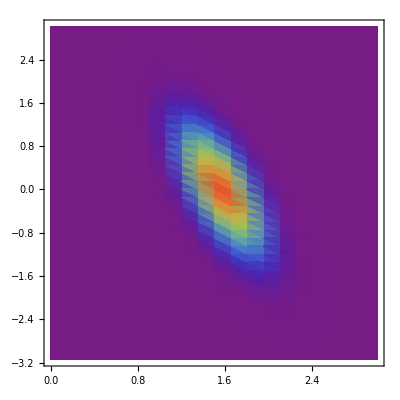

```mathematica
ListDensityPlot[data,PlotRange->All,ColorFunction->"Rainbow",ColorFunctionScaling->False]
```